## 2. Collatz and Variants

```mathematica
(*a)*)
variante[fpar_, fimpar_, n_Integer] := 
Module[{listaCollatz, iter , m },
listaCollatz = {n};
iter = 0;
m =Last[listaCollatz];

While[iter<=20 && m != 1,If[ EvenQ[m], AppendTo[listaCollatz, fpar[m]],AppendTo[listaCollatz, fimpar[m]]]; 
iter= iter + 1; m =Last[listaCollatz]]; 
Return[listaCollatz]
];
```

```mathematica
(*b)*)
Par[x_]:= x/2;
Impar[x_] := 3*x+1
Collatz[t_] := variante[Par, Impar, t]

Collatz[7]
Collatz[50]
Collatz[64]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

{50,25,76,38,19,58,29,88,44,22,11,34,17,52,26,13,40,20,10,5,16,8}

{64,32,16,8,4,2,1}

```mathematica
*c)*)
Remove[Impar]
Impar[x_] := 2*x + 1 

variante[Par, Impar, 7]
variante[Par, Impar, 23]
variante[Par, Impar, 12]
variante[Par, Impar, 3]
```

```mathematica
Remove[Impar]
Impar[x_] := 6*x + 1 

variante[Par, Impar, 7]
variante[Par, Impar, 23]
variante[Par, Impar, 12]
variante[Par, Impar, 3]
```

{7,43,259,1555,9331,55987,335923,2015539,12093235,72559411,435356467,2612138803,15672832819,94036996915,564221981491,3385331888947,20311991333683,121871948002099,731231688012595,4387390128075571,26324340768453427,157946044610720563}

{23,139,835,5011,30067,180403,1082419,6494515,38967091,233802547,1402815283,8416891699,50501350195,303008101171,1818048607027,10908291642163,65449749852979,392698499117875,2356190994707251,14137145968243507,84822875809461043,508937254856766259}

{12,6,3,19,115,691,4147,24883,149299,895795,5374771,32248627,193491763,1160950579,6965703475,41794220851,250765325107,1504591950643,9027551703859,54165310223155,324991861338931,1949951168033587}

{3,19,115,691,4147,24883,149299,895795,5374771,32248627,193491763,1160950579,6965703475,41794220851,250765325107,1504591950643,9027551703859,54165310223155,324991861338931,1949951168033587,11699707008201523,70198242049209139}

```mathematica
(*d)*)
	(*i*)
cima[a_, b_] :=
Circle[{((a+b)/2), 0}, Abs[(b-a)]/2,{0, Pi}];

baixo[a_, b_] :=
Circle[{(a+b)/2, 0}, Abs[(b-a)]/2, {Pi, 2*Pi}];
```

```mathematica
(*ii*) 

semicirculos[l_List] := Module[{gdata, iter}, 
iter = 1;
gdata = {};

While[ iter < Length[l], 
If[OddQ[iter], AppendTo[gdata,cima[l[[iter]], l[[iter+1]]]],AppendTo[gdata,baixo[l[[iter]], l[[iter+1]]]]
]; iter = iter +1];
Graphics[gdata,Axes->{True,False},AxesStyle->Pink]
];
```

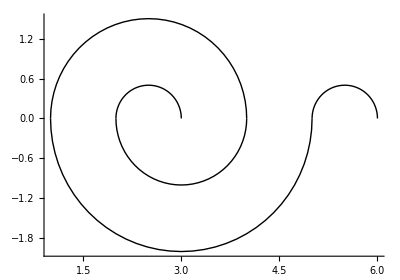

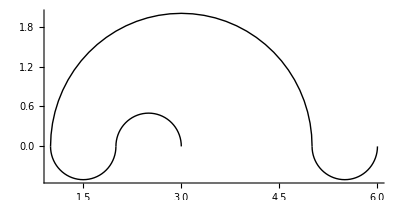

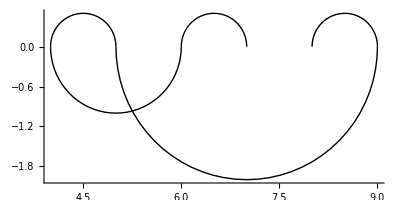

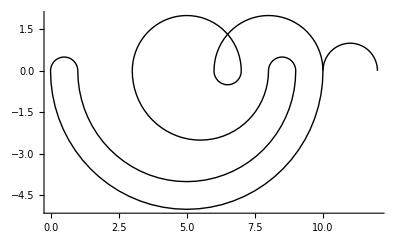

```mathematica
semicirculos[{3,2,4,1,5,6}]
semicirculos[{3,2,1,5,6}]
semicirculos[{8,9,5,4,6,7}]
semicirculos[{10,6,7,3,8,9,1,0,10,12}]
```

```mathematica
(*iii*)
visualizar[par_, impar_, n_Integer] := Module[{listaCollatz},
listaCollatz = variante[par, impar, n];
Return[semicirculos[listaCollatz]]
];
```

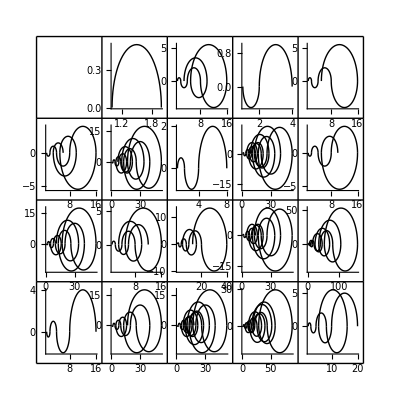

```mathematica
(*e)*)
Remove[Impar]
Impar[x_] := 3*x+1

Show[ GraphicsGrid[Table[visualizar[Par, Impar, x+y], {x, 1, 20, 5}, {y, 0, 4}], 
Frame -> All, AspectRatio -> 1]]
```

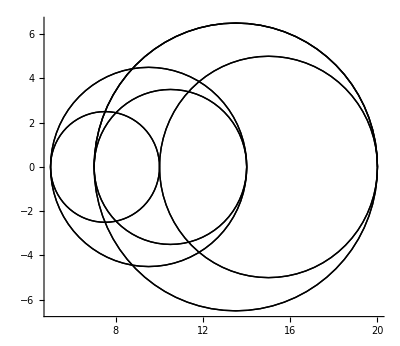

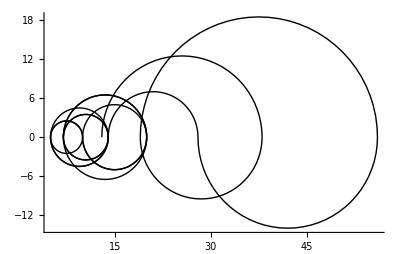

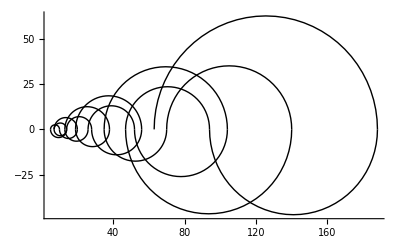

```mathematica
(*f)*)
	(*i*)
		Remove[Par]
		Remove[Impar]
		Par[x_] := x/2
		Impar[x_] := 3*x-1
		
		visualizar[Par, Impar, 7]
		visualizar[Par, Impar, 13]
		visualizar[Par, Impar, 63]
```

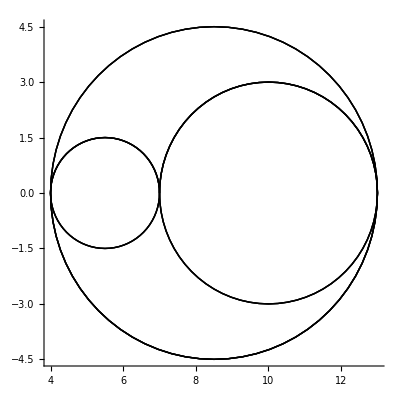

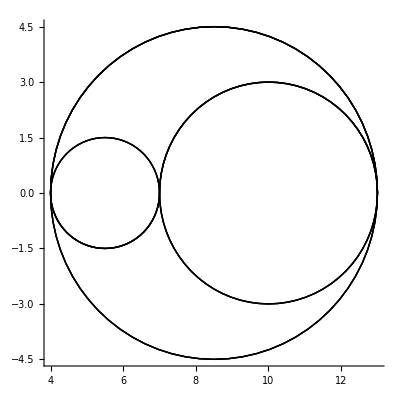

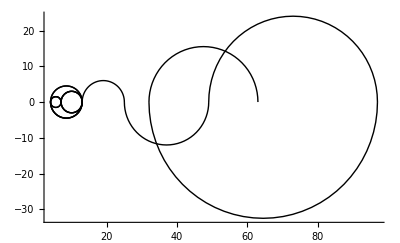

```mathematica
(*ii*)
		Remove[Par]
		Remove[Impar]
		Par[x_] := 3*x+1
		Impar[x_] := (x+1)/2
		
		visualizar[Par, Impar, 7]
		visualizar[Par, Impar, 13]
		visualizar[Par, Impar, 63]
```

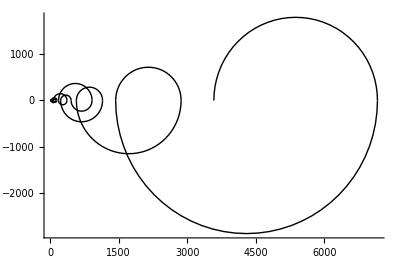

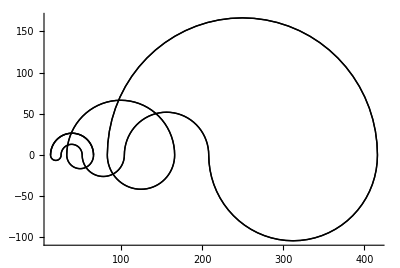

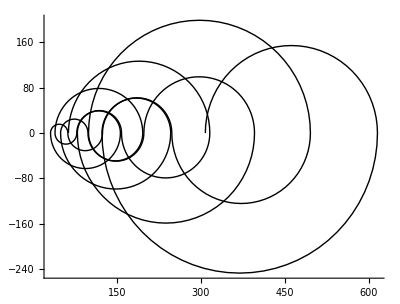

```mathematica
(*iii*)
		Remove[Par]
		Remove[Impar]
		Par[x_] := x/2
		Impar[x_] := (5*x)+1
		
		visualizar[Par, Impar, 7]
		visualizar[Par, Impar, 13]
		visualizar[Par, Impar, 63]
```

## 3. Factorial Basis

```mathematica
(*a)*)
fromfacbase[l_List]:= Module[{fact, res, lista},
fact = 1;
res = 0;
lista = l;
While[Length[lista]!= 0,
res = res + Last[lista]* fact!;
fact= fact + 1; (lista = Drop[lista, -1])];
Return[res];
];

fromfacbase[{1,0,0}]
fromfacbase[{2,1}]
```

6

5

```mathematica
listaFactorial[x_Integer] := Module[{resfact,factn, n},
n=1;
resfact= {};
factn = n!;
(*Formar lista de possíveis fatoriais*)
While[(factn)<=x, AppendTo[resfact, factn]; n =n+1;factn = n!];
Return[resfact];
];
```

```mathematica
(*b)*)
facbase[x_Integer] := Module[{facExp, factlist, n, m, i, last},
n=x;
factlist = listaFactorial[x];
facExp = {};
If[x==0, Return[List[0]]];
If [Length[factlist]!=0,
While[fromfacbase[facExp]!= x,last = Last[factlist];i=0; m=0;
While[m+last<= n, m = m+last];  i=i + m/last; 
AppendTo[facExp, i] ;factlist = Select[factlist, #<last&]; n = n - m; 
];
Return[facExp];
]];
```

```mathematica
facbase[1]
facbase[6]
facbase[10]
facbase[25]
facbase[100]
```

{1}

{1,0,0}

{1,2,0}

{1,0,0,1}

{4,0,2,0}

```mathematica
facbase0[x_Integer] := Module[{facExp, factlist, n, m, i, last, k, facExp0},
k= x;
n=x;
factlist = listaFactorial[x];
facExp = {};
If[x==0, Return[List[0]]];
If [Length[factlist]!=0,
While[fromfacbase[facExp]!= k ,last = Last[factlist];i=0; m=0;
While[m+last<= n, m = m+last];  i=i + m/last; 
AppendTo[facExp, i] ;factlist = Select[factlist, #<last&]; n = n - m; 
];
facExp0=Join[facExp, List[0]];
Return[facExp0];
]];
```

```mathematica
facbase[13]
facbase0[13]
```

{2,0,1}

{2,0,1,0}

```mathematica
(*c)*)
Lfacbase = Map[facbase, Range[1000]] ;
Map[fromfacbase, Lfacbase] == Range[1000]
```

True

```mathematica
(*d)*)
fromfacbasefrac[l_List] := Module[{ind, res, lista},
ind = 1;
res = 0;
lista = l;
While[Length[lista]!= 0,
res = res + Last[lista]* 1/(ind!);
ind = ind + 1; (lista = Drop[lista, -1])];
Return[res];
];
```

```mathematica
facbasefrac[x_] := Module[{i, facExp, n, fact, m, factfrac},
facExp = {};
n = x;
i=0;
fact = 1;
m= 0;
factfrac = 1/(fact!);
While[fromfacbasefrac[facExp]!= x &&  Length[facExp]<30,i=0;m=0;
While[m+factfrac<= n, m = m+factfrac];  i=i + m/factfrac; fact = fact +1;
AppendTo[facExp, i] ; n = n - m; factfrac = 1/(fact!);
];
Return[facExp];
];
```

```mathematica
facbasefrac[1/2]
facbasefrac[1/3]
facbasefrac[1/10]
```

{0,1,0}

{0,0,2,0,0}

{0,0,0,2,2,0,0,0}

```mathematica
(*e)*)fullfacbase[x_, k_Integer ] := Module[{fullfacExp, nInt, intExp, nFrac, fracExp, i, j},
i =0;
nInt = Floor[x];
If[nInt <= 0, intExp = List[0], intExp = facbase[nInt]];
nFrac = x - nInt;
fracExp = facbasefrac[nFrac];
j= Length[fracExp];
While[j!= k , 
If[Length[fracExp]< k , AppendTo[fracExp, 0], fracExp=Delete[fracExp, -1]];i = i+1; j= Length[fracExp];];

fullfacExp = Join[intExp, {"."}, fracExp];
Return[fullfacExp];
];
```

```mathematica
fullfacbase[5/2, 7]
fullfacbase[7/3, 6]
fullfacbase[21/10, 10]
```

{1,0,.,0,1,0,0,0,0,0}

{1,0,.,0,0,2,0,0,0}

{1,0,.,0,0,0,2,2,0,0,0,0,0}

```mathematica
(*h)*)
fullfacbase[ⅇ, 30]
fullfacbase[(1/ⅇ), 30]
fullfacbase[Sin[1], 30]
fullfacbase[Cos[1], 30]
fullfacbase[Sinh[1], 30]
fullfacbase[Cosh[1], 30]
```

{1,0,.,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{0,.,0,0,2,0,4,0,6,0,8,0,10,0,12,0,14,0,16,0,18,0,20,0,22,0,24,0,26,0,28,0}

{0,.,0,1,2,0,0,5,6,0,0,9,10,0,0,13,14,0,0,17,18,0,0,21,22,0,0,25,26,0,0,29}

{0,.,0,1,0,0,4,5,0,0,8,9,0,0,12,13,0,0,16,17,0,0,20,21,0,0,24,25,0,0,28,29}

{1,.,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}

{1,.,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

```mathematica
(*h)*)
fullfacbase[N[ⅇ], 30]
fullfacbase[N[(1/ⅇ)], 30]
fullfacbase[N[Sin[1]], 30]
fullfacbase[N[Cos[1]], 30]
fullfacbase[N[Sinh[1]], 30]
fullfacbase[N[Cosh[1]], 30]
$MachinePrecision
```

{1,0,.,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,.,0,0,2,0,4,0,6,0,8,0,10,0,12,0,14,0,16,1,2,17,1,10,15,10,14,15,18,25,6,23}

{0,.,0,1,2,0,0,5,6,0,0,9,10,0,0,13,14,0,1,0,1,1,8,17,13,8,12,14,6,13,26,22}

{0,.,0,1,0,0,4,5,0,0,8,9,0,0,12,13,0,0,16,17,5,18,18,13,17,4,24,8,8,7,7,14}

{1,.,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,17,11,11,18,2,16,23,21,24,8,11,20,27}

{1,.,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

15.9546